```mathematica
T[En_,Th_,V_]:=(4*Cos[Th]*(En*(En*Cos[Th]^2+V))^(1/2))/((En^(1/2)*Cos[Th]+(En*Cos[Th]^2+V)^(1/2))^2)
```

```mathematica
A=Table[{
N[Th],
NIntegrate[T[En,Th,4.25],{En,0,0.5}],
NIntegrate[T[En,Th,4.25],{En,0,0.2}],
0.3*Cos[Th]
},{Th,-π/2,π/2,π/100}];
(*ListPlot[A]*)
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

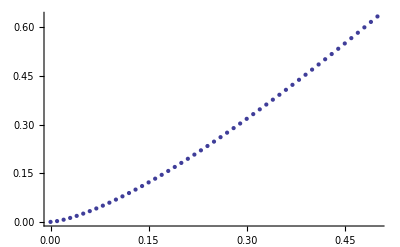

```mathematica
B=Table[{En,NIntegrate[T[Eh,Th,4.25],{Th,-π/2,π/2},{Eh,0,En}]},{En,0,0.5,0.01}];
ListPlot[B]
```

```mathematica
Export[StringJoin[NotebookDirectory[],"Angle.csv"],A]
```

/home/joel/Documents/workspace/Prelim_Talk/other/Angle.csv

```mathematica
Export[StringJoin[NotebookDirectory[],"Energy.csv"],B]
```

/home/joel/Documents/workspace/Prelim_Talk/other/Energy.csv